```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 385 Kb

{Utilities`CleanSlate`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`}

```mathematica
Clear[s]
s = { x[t] + r Sin[θ[t]] , r + r Cos[θ[t]] }
```

{r Sin[θ[t]]+x[t],r+r Cos[θ[t]]}

```mathematica
D[s, t]
```

{x'[t]+r Cos[θ[t]] θ'[t],-r Sin[θ[t]] θ'[t]}

```mathematica
D[s, t] . D[s, t]
```

r^2 Sin[θ[t]]^2 θ'[t]^2+(x'[t]+r Cos[θ[t]] θ'[t])^2

```mathematica
D[s, t] . D[s, t]  // Expand
```

x'[t]^2+2 r Cos[θ[t]] x'[t] θ'[t]+r^2 Cos[θ[t]]^2 θ'[t]^2+r^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[s, t] . D[s, t]  // Expand // Simplify
```

x'[t]^2+2 r Cos[θ[t]] x'[t] θ'[t]+r^2 θ'[t]^2

```mathematica
Clear[X,x]
X = 
x[t] == r θ[t]
```

x[t]==r θ[t]

```mathematica
D[X, t]
```

x'[t]==r θ'[t]

```mathematica
Clear[θtReplace]
θtReplace = 
Flatten[Solve[ D[X, t]  , θ'[t] ] ]
```

{θ'[t]→x'[t]/r}

```mathematica
Clear[T]
T = 1/2 m ( D[s, t] . D[s, t]  // Expand // Simplify  ) + 1/2 M x'[t]^2 +(  1/2( M r^2 ) θ'[t]^2 //. θtReplace )
```

M x'[t]^2+1/2 m (x'[t]^2+2 r Cos[θ[t]] x'[t] θ'[t]+r^2 θ'[t]^2)

```mathematica
Clear[V]
V = m g ( r + r Cos[θ[t]] )
```

g m (r+r Cos[θ[t]])

```mathematica
Clear[ℒ]
ℒ = T - V
```

-g m (r+r Cos[θ[t]])+M x'[t]^2+1/2 m (x'[t]^2+2 r Cos[θ[t]] x'[t] θ'[t]+r^2 θ'[t]^2)

```mathematica
Clear[q]
q = { x[t] , θ[t] }
```

{x[t],θ[t]}

```mathematica
D[ D[ ℒ , D[q[[1]], t] ] , t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ , D[q[[2]], t] ] , t ] - D[ ℒ , q[[2]] ]
```

2 M x''[t]+1/2 m (-2 r Sin[θ[t]] θ'[t]^2+2 x''[t]+2 r Cos[θ[t]] θ''[t])

-g m r Sin[θ[t]]+m r Sin[θ[t]] x'[t] θ'[t]+1/2 m (-2 r Sin[θ[t]] x'[t] θ'[t]+2 r Cos[θ[t]] x''[t]+2 r^2 θ''[t])

```mathematica
Table[
D[ D[ ℒ , D[q[[i]], t] ] , t ] - D[ ℒ , q[[i]] ]== 0  , 
{ i, 1,2 } ]// Simplify  // TableForm
```

m r Sin[θ[t]] θ'[t]^2==(m+2 M) x''[t]+m r Cos[θ[t]] θ''[t]
m r (-g Sin[θ[t]]+Cos[θ[t]] x''[t]+r θ''[t])==0

```mathematica
Clear[eqs]
eqs = 
EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

m r Sin[θ[t]] θ'[t]^2-(m+2 M) x''[t]-m r Cos[θ[t]] θ''[t]==0
-m r (-g Sin[θ[t]]+Cos[θ[t]] x''[t]+r θ''[t])==0

```mathematica
Clear[com]
com = 
FirstIntegrals[ ℒ , q, t ] ; 
com // TableForm
```

FirstIntegral[x]→-(m+2 M) x'[t]-m r Cos[θ[t]] θ'[t]
FirstIntegral[t]→(m/2+M) x'[t]^2+m r Cos[θ[t]] x'[t] θ'[t]+1/2 m r (2 g (1+Cos[θ[t]])+r θ'[t]^2)

```mathematica
D[ ℒ , D[q[[1]], t] ] // Simplify
```

(m+2 M) x'[t]+m r Cos[θ[t]] θ'[t]

```mathematica
Clear[parameters]
parameters = 
{ 
M-> 50 ,
m -> 5 ,
r -> 2 , 
g -> 9.8 
} ;
parameters // TableForm
```

M→50
m→5
r→2
g→9.8

```mathematica
eqs /. parameters  // TableForm
```

10 Sin[θ[t]] θ'[t]^2-105 x''[t]-10 Cos[θ[t]] θ''[t]==0
-10 (-9.8 Sin[θ[t]]+Cos[θ[t]] x''[t]+2 θ''[t])==0

```mathematica
Clear[ics]
ics = { 
x[0] == 0 ,
x'[0] == 0 ,
θ[0] == 0 ,
θ'[0] == 10 
} ;
ics // TableForm
```

x[0]==0
x'[0]==0
θ[0]==0
θ'[0]==10

```mathematica
Clear[solution]
solution = 
NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 10 } ]
```

{{x[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}}

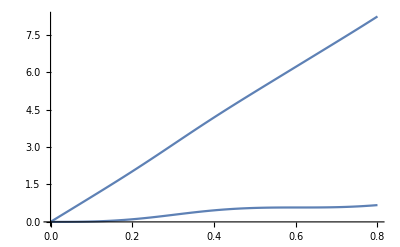

```mathematica
Plot[ q /. solution , { t, 0, 0.8 } ]
```

```mathematica
Exit[]
Quit[]
```